```mathematica
l2nest = Import["/Users/mcarnright/ANN/IDENITY/l2.csv","Table","FieldSeparators"->","]
```

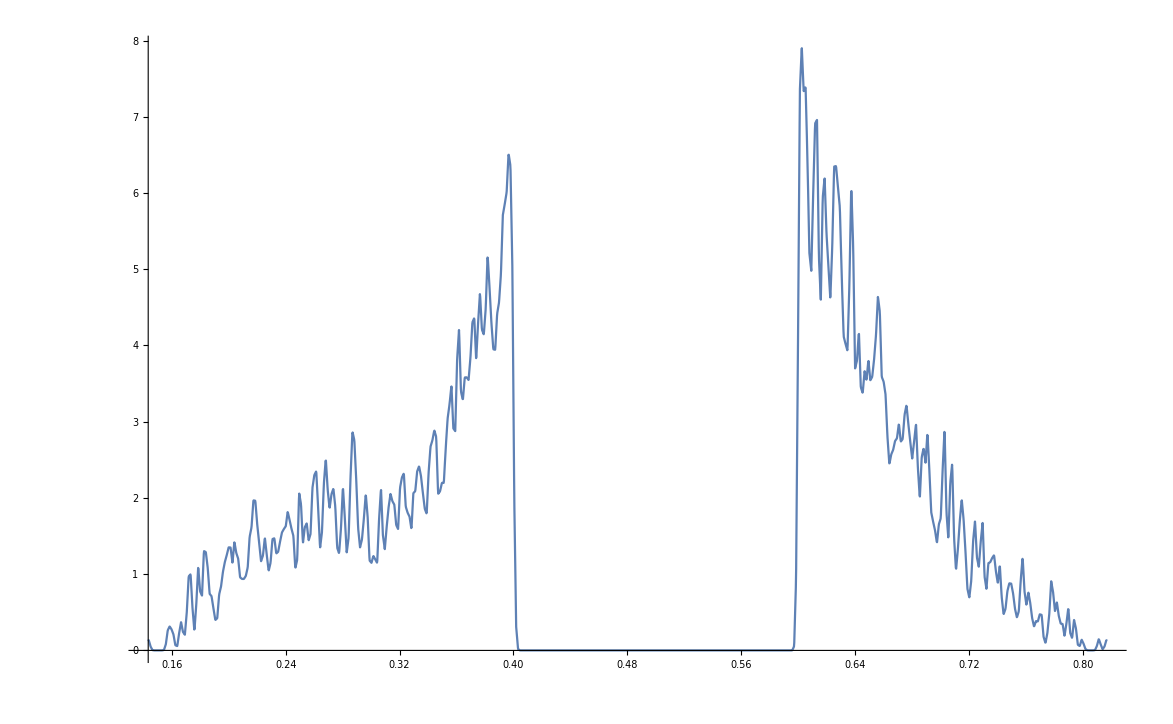

```mathematica
Plot[Evaluate@PDF[SmoothKernelDistribution[l2,.001],x],{x,Min[l2],Max[l2]}]
```

```mathematica
DensityPlot[Evaluate[{PDF[SmoothKernelDistribution[l2,.001],x],0}],{x,Min[l2],Max[l2]},{y,0,.05},AspectRatio->Automatic,PlotPoints->{1000,20}]
```

-Graphics-

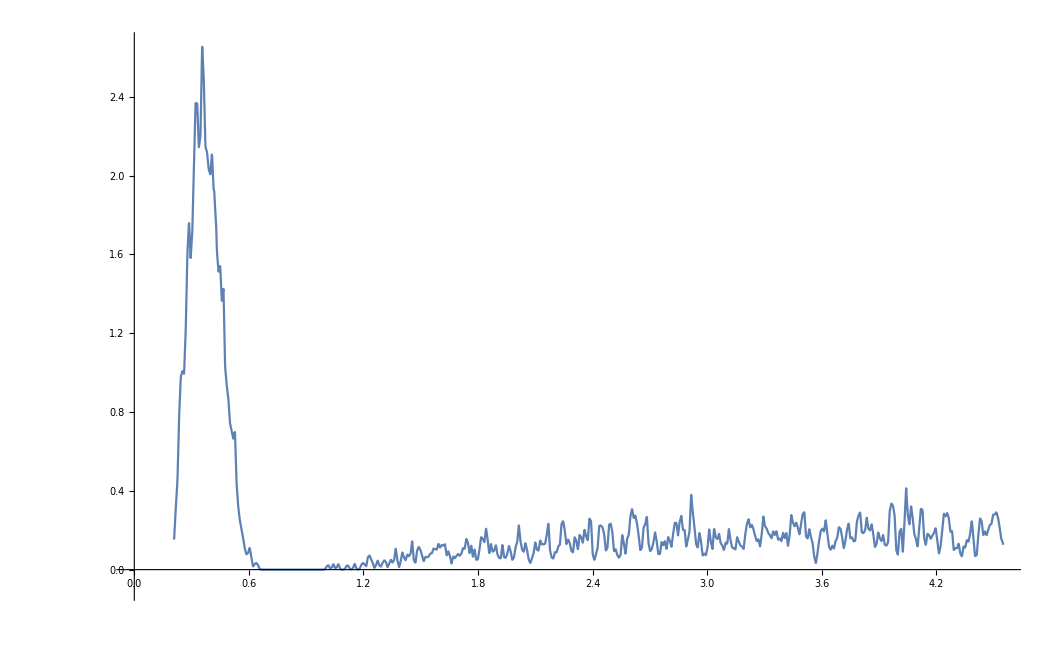

```mathematica
Plot[Evaluate@PDF[SmoothKernelDistribution[syn0,.005],x],{x,Min[syn0],Max[syn0]},PlotRange->{-.1,2.67}]
```

```mathematica
DensityPlot[Evaluate[{PDF[SmoothKernelDistribution[syn0,.005],x],0}],{x,Min[syn0],Max[syn0]},{y,0,.01},AspectRatio->Automatic,PlotPoints->{1000,20},PlotRange->{0,6}]
```

-Graphics-

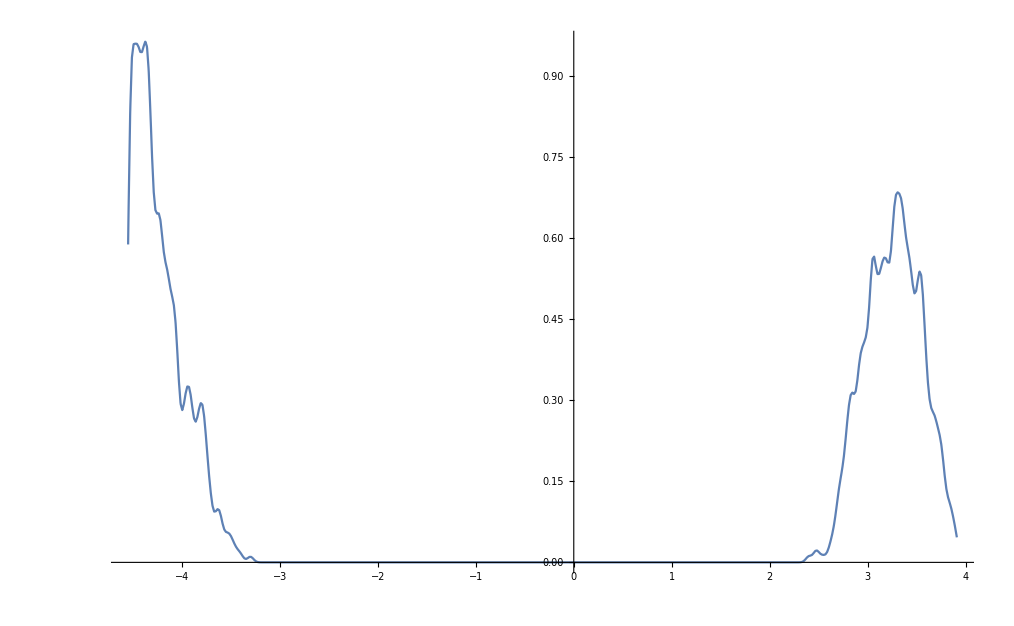

```mathematica
Plot[Evaluate@PDF[SmoothKernelDistribution[syn1,.03],x],{x,Min[syn1],Max[syn1]}]
```

```mathematica
DensityPlot[Evaluate[{PDF[SmoothKernelDistribution[syn1,.005],x],0}],{x,Min[syn1],Max[syn1]},{y,0,.05},AspectRatio->Automatic,PlotPoints->{1000,20}]
```

-Graphics-